```mathematica
ClearAll[No]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);us=10^(-6);
A=4*Pi*r*r; (*Area*)
Subscript[I, sat]=25.03 ;(*Saturation intensity (SI unit)*)
λ=(1560.0698/2)nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
g=9.81;
tof=5ms;
detuning=100GHz;
radius=8mm;
n=2;
λrb=(1560.482418/2)nm;
Δ=101.59705 GHz;
(λrb-λ)/nm
Ω12[In_,r_]=In*Γ*Γ/(Subscript[I, sat] *4*Δ)*1;

(2*g*tof/λ) +ℏ*k*k/(m*Pi)
```

0.206309

140856.

```mathematica
Frequency difference
```

```mathematica
(2*g*tof/λ) +ℏ*k*k/(m*Pi)
```

140856.

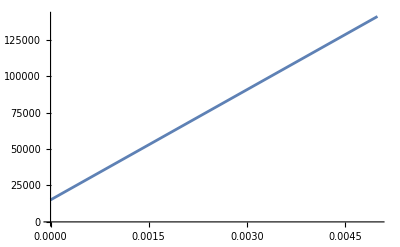

```mathematica
Plot[(2*g*x/λ) +ℏ*k*k/(m*Pi),{x,0,5ms}]
```

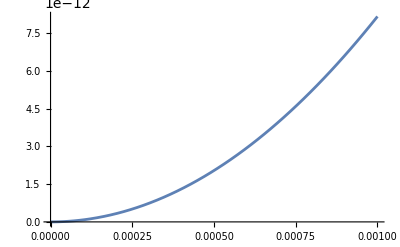

```mathematica
Plot[((Sin[Ω12[in,0]*40us/2])^2),{in,0,ms},PlotRange->All]
```

```mathematica
Solve[Ω12[in,0]== 40us*Pi*0.5]
```

{{in→4.40109×10^-7}}

```mathematica
4.4*10^(-7)*Pi*radius*radius*0.5
```

4.42336×10^-11

```mathematica
power=0.250
Ω12[power*2/(Pi*radius*radius),0]/(40us)
```

0.25

8.87564×10^9